```mathematica
K2meV=0.086173324;
K2eV=K2meV/1000;
```

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/FREN/order3"];
fileFFE={"e0.out.m","e0_fs.out.m","VFE.Fqh_FS.out.m","VFE.Fel_Fqh_FS.out.m"};
FFEdata=Table[ReadList[fileFFE[[i]],{Number, Number,Number,Number,Number,Number}],{i,1,4}];
FFEdata[[4]]//Dimensions
```

{4000,6}

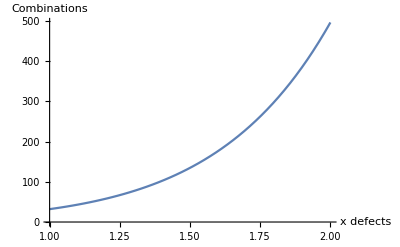

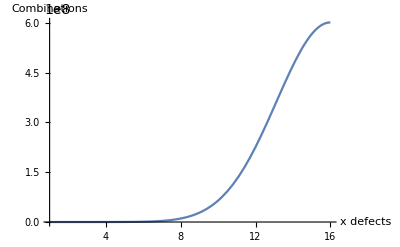

```mathematica
(*How many ways can I count x defects on 32 sites*)
f[x_]:=32!/((32-x)!*x!)
Plot[f[x],{x,1,2},AxesLabel->{"x defects","Combinations"}]
Plot[f[x],{x,1,16},AxesLabel->{"x defects","Combinations"}]
```

```mathematica
(*T_Kelvin FREN_1126_eVperD FREN_129_eVperD FREN_142_eVperD FREN_174_eVperD FREN_70_eVperD*)

(*1=1126=U4, 2=129=B2, 3=142=B3, 4=174=U3,5=70=U2 *)
```

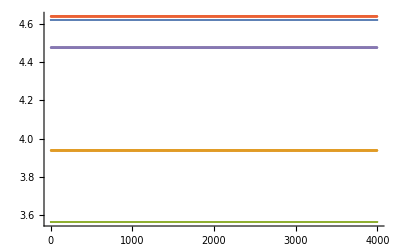

```mathematica
ListPlot@Transpose[FFEdata[[1]]][[2;;6]]
```

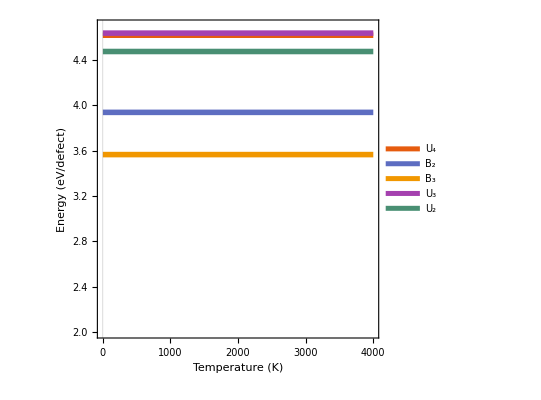

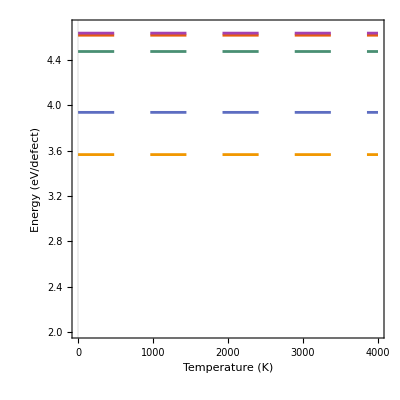

```mathematica
G1=ListLinePlot[Transpose[FFEdata[[1]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.01],FrameTicksStyle->18,Frame->True,ImageSize->400,PlotTheme->Scientific,PlotLegends->{Style["U_4",20,Black],Style["B_2",20,Black],Style["B_3",20,Black],Style["U_3",20,Black],Style["U_2",20,Black]}]
G1a=ListLinePlot[Transpose[FFEdata[[1]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},PlotTheme->Scientific,FrameLabel->{Style["Temperature (K)",18,Black],Style["Energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Thickness[0.005],Dashing[0.065]],FrameTicksStyle->18,Frame->True,ImageSize->400]
```

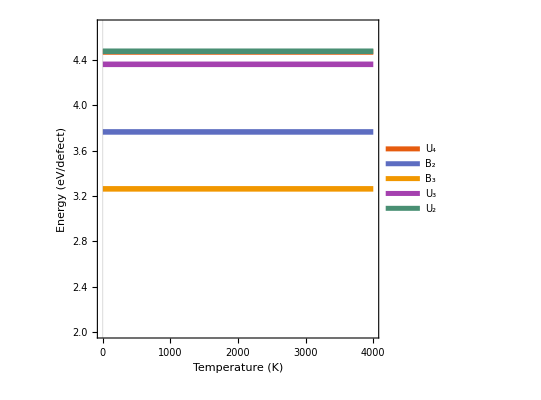

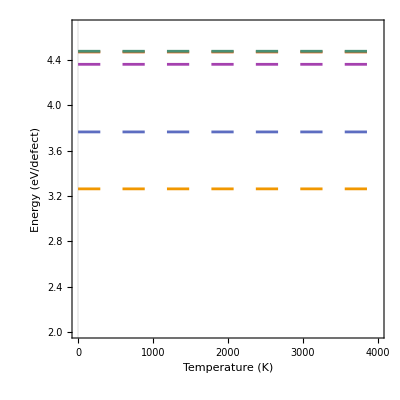

```mathematica
G2=ListLinePlot[Transpose[FFEdata[[2]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},PlotTheme->Scientific,FrameLabel->{Style["Temperature (K)",18,Black],Style["Energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.01],FrameTicksStyle->18,Frame->True,ImageSize->400,PlotLegends->{Style["U_4",20,Black],Style["B_2",20,Black],Style["B_3",20,Black],Style["U_3",20,Black],Style["U_2",20,Black]}]
G2a=ListLinePlot[Transpose[FFEdata[[2]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},PlotTheme->Scientific,FrameLabel->{Style["Temperature (K)",18,Black],Style["Energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Thickness[0.005],Dashing[0.04]],FrameTicksStyle->18,Frame->True,ImageSize->400]
```

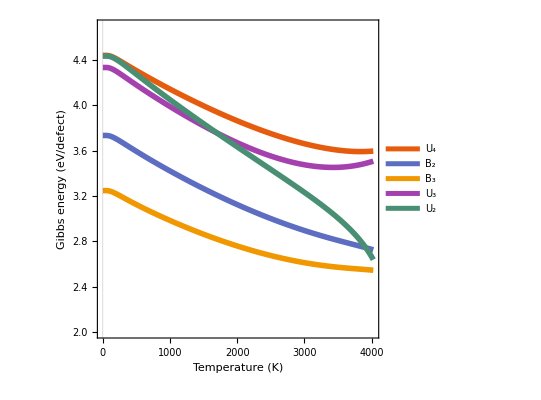

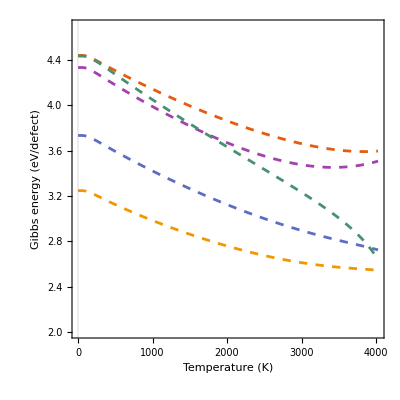

```mathematica
G3=ListLinePlot[Transpose[FFEdata[[3]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Gibbs energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.01],FrameTicksStyle->18,Frame->True,ImageSize->400,PlotTheme->Scientific,PlotLegends->{Style["U_4",20,Black],Style["B_2",20,Black],Style["B_3",20,Black],Style["U_3",20,Black],Style["U_2",20,Black]}]
G3a=ListLinePlot[Transpose[FFEdata[[3]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},PlotTheme->Scientific,FrameLabel->{Style["Temperature (K)",18,Black],Style["Gibbs energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Thickness[0.005],Dashing[0.015]],FrameTicksStyle->18,Frame->True,ImageSize->400]
```

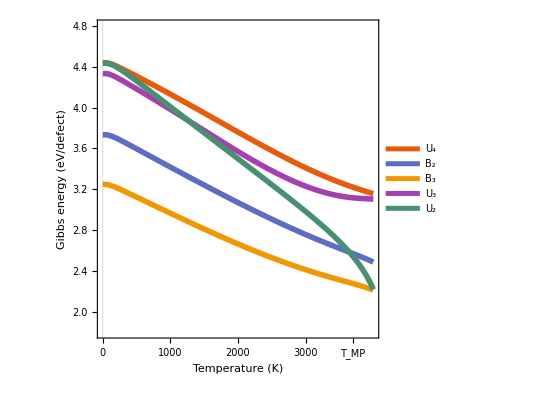

```mathematica
G4=ListLinePlot[Transpose[FFEdata[[4]]][[2;;6]],PlotRange->{Automatic,{1.8,4.8}},PlotTheme->Scientific,FrameLabel->{Style["Temperature (K)",18,Black],Style["Gibbs energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.01],FrameTicksStyle->18,FrameTicks->{Automatic,{{0,1000,2000,3000,{3700,"T_MP"}},None}},Frame->True,ImageSize->400,PlotLegends->Placed[{Style["U_4",20,Black],Style["B_2",20,Black],Style["B_3",20,Black],Style["U_3",20,Black],Style["U_2",20,Black]},{0.12,0.22}]]
G4a=ListLinePlot[Transpose[FFEdata[[4]]][[2;;6]],PlotRange->{Automatic,{1.8,4.8}},PlotTheme->Scientific,FrameLabel->{Style["Temperature (K)",18,Black],Style["Gibbs energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Thickness[0.005],Dashing[0.015]],FrameTicksStyle->18,Frame->True,ImageSize->400];
```

```mathematica
GraphicsGrid[{{Show[G1],
Show[{G2,G1a}]},{
Show[{G3,G2a,G1a}],
Show[{G4,G3a,G2a,G1a}]}},ImageSize->1200];
```

```mathematica
(*gibbsDefects=Show[{G4,G3a,G2a,G1a},PlotRange->{{0,3000},{1.5,5}}]*)
```

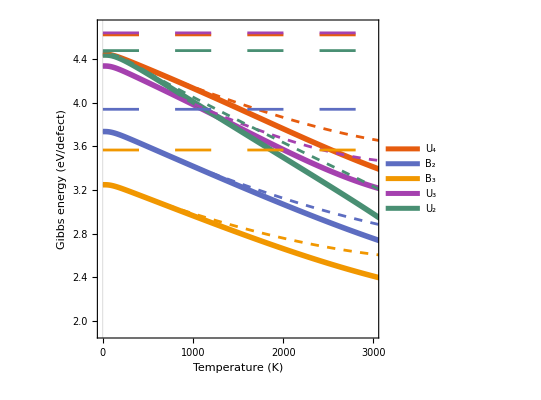

```mathematica
gibbsDefects=Show[{G4,G3a,G1a},PlotRange->{{0,3000},{1.9,4.7}}]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/gibbsDefects.pdf",gibbsDefects]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/gibbsDefects.pdf

```mathematica
.
```

```mathematica
(*T_Kelvin FREN_1126_eVperD FREN_129_eVperD FREN_142_eVperD FREN_174_eVperD FREN_70_eVperD*)

(*1=1126=U4, 2=129=B2, 3=142=B3, 4=174=U3,5=70=U2 *)
```

```mathematica
(*T_Kelvin FREN_1126_eVperD FREN_129_eVperD FREN_142_eVperD FREN_174_eVperD FREN_70_eVperD*)
```

```mathematica
gibbsData=FFEdata[[4]];
mB3=24;
mB2=24;
mU2=3;
mU3=12;
mU4=12;
temperature=Transpose[gibbsData][[1]];
gibbsU4=Transpose[gibbsData][[2]];
gibbsB2=Transpose[gibbsData][[3]];
gibbsB3=Transpose[gibbsData][[4]];
gibbsU3=Transpose[gibbsData][[5]];
gibbsU2=Transpose[gibbsData][[6]];

(*1126=U4, 129=B2, 142=B3, 174=U3, 70=U2*)
```

```mathematica
styles=Flatten@Join[{Directive[{Thickness[0.008]}],Table[Directive[{Thickness[0.01],Dashing[{0.02*i,0.04}]}],{i,1,3}],Directive[{Thickness[0.008],Dotted}],Directive[{Thickness[0.01],DotDashed}]}];
```

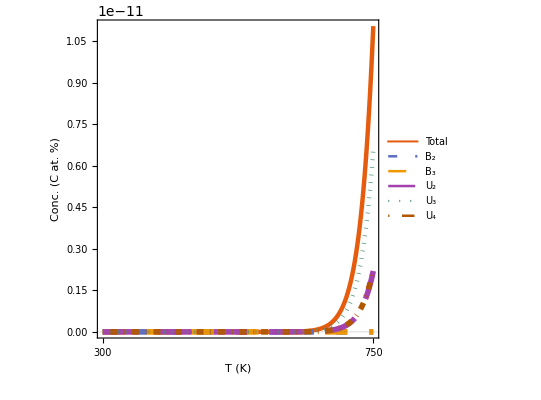

```mathematica
upper=750;
lower=300;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};
p0=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["Conc. (C at. %)",18,Black]},Frame->True,ImageSize->400,PlotTheme->Scientific,PlotLegends->Placed[{Style["Total",18,Black],Style["B_2",18,Black],Style["B_3",18,Black],Style["U_2",18,Black],Style["U_3",18,Black],Style["U_4",18,Black]},{0.25,0.55}],AspectRatio->1,PlotRange->All,FrameTicks->{{Automatic,None},{{300,750},None}}]
```

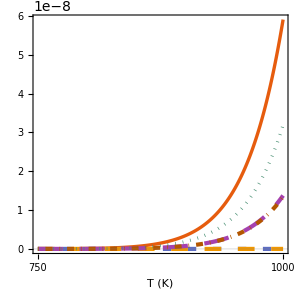

```mathematica
upper=1000;
lower=750;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};
p1=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["",18,Black]},Frame->True,ImageSize->300,PlotTheme->Scientific,AspectRatio->1,PlotRange->All,FrameTicks->{{Automatic,None},{{750,1000},None}}]
```

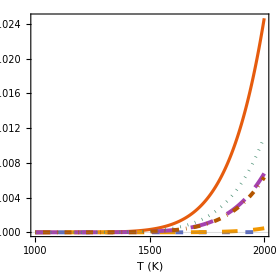

```mathematica
upper=2000;
lower=1000;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};
p2=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["",18,Black]},Frame->True,ImageSize->280,AspectRatio->1,PlotRange->All,FrameTicks->{{Automatic,None},{{1000,1500,2000},None}}]
```

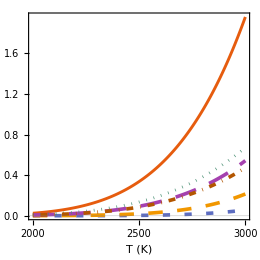

```mathematica
upper=3000;
lower=2000;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};
p3=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["",18,Black]},Frame->True,ImageSize->260,AspectRatio->1,PlotRange->All,FrameTicks->{{Automatic,None},{{2000,2500,3000},None}}]
```

```mathematica
0.27
```

0.27

```mathematica
concB2[[-501]]
```

{2500,0.00332932}

```mathematica
"2000K - bound and unbound concs, 0% vac"
{concB2[[1]]+concB3[[1]]}[[1]][[2]]
{concU2[[1]]+concU3[[1]]+concU4[[1]]}[[1]][[2]]
{concU2[[1]]+concU3[[1]]+concU4[[1]]}[[1]][[2]]+{concB2[[1]]+concB3[[1]]}[[1]][[2]]
"2000K - bound and unbound concs, 5%"
{concB2[[1]]+concB3[[1]]}[[1]][[2]]/(1+0.05)
{concU2[[1]]+concU3[[1]]+concU4[[1]]}[[1]][[2]]/(1+0.05)^0.5
{concU2[[1]]+concU3[[1]]+concU4[[1]]}[[1]][[2]]/(1+0.05)^0.5+{concB2[[1]]+concB3[[1]]}[[1]][[2]]/(1+0.05)^0.5
"2000K - bound and unbound concs, 10%"
{concB2[[1]]+concB3[[1]]}[[1]][[2]]/(1+0.1)
{concU2[[1]]+concU3[[1]]+concU4[[1]]}[[1]][[2]]/(1+0.1)^0.5
{concU2[[1]]+concU3[[1]]+concU4[[1]]}[[1]][[2]]/(1+0.1)^0.5+{concB2[[1]]+concB3[[1]]}[[1]][[2]]/(1+0.1)
```

2000K - bound and unbound concs, 0% vac

0.000514105

0.0241338

0.0246479

2000K - bound and unbound concs, 5%

0.000489624

0.0235522

0.0240539

2000K - bound and unbound concs, 10%

0.000467368

0.0230107

0.0234781

```mathematica
NumberForm[0.023478060840525332,16]
```

0.02347806084052533

```mathematica
6343/30//N
```

211.433

```mathematica
0.46787527180785454/0.4912690353982473
```

0.952381

```mathematica
"2500K - bound and unbound concs, 0% vac"
{concB2[[-501]]+concB3[[-501]]}[[1]][[2]]
{concU2[[-501]]+concU3[[-501]]+concU4[[-501]]}[[1]][[2]]
{concU2[[-501]]+concU3[[-501]]+concU4[[-501]]}[[1]][[2]]+{concB2[[-501]]+concB3[[-501]]}[[1]][[2]]
"2500K - bound and unbound concs, 5%"
{concB2[[-501]]+concB3[[-501]]}[[1]][[2]]/(1+0.05)
{concU2[[-501]]+concU3[[-501]]+concU4[[-501]]}[[1]][[2]]/(1+0.05)^0.5
{concU2[[-501]]+concU3[[-501]]+concU4[[-501]]}[[1]][[2]]/(1+0.05)^0.5+{concB2[[-501]]+concB3[[-501]]}[[1]][[2]]/(1+0.05)
"2500K - bound and unbound concs, 10%"
{concB2[[-501]]+concB3[[-501]]}[[1]][[2]]/(1+0.1)
{concU2[[-501]]+concU3[[-501]]+concU4[[-501]]}[[1]][[2]]/(1+0.1)^0.5
{concU2[[-501]]+concU3[[-501]]+concU4[[-501]]}[[1]][[2]]/(1+0.1)^0.5+{concB2[[-501]]+concB3[[-501]]}[[1]][[2]]/(1+0.1)
```

2500K - bound and unbound concs, 0% vac

0.02258

0.314363

0.336943

2500K - bound and unbound concs, 5%

0.0215047

0.306787

0.328292

2500K - bound and unbound concs, 10%

0.0205272

0.299734

0.320261

```mathematica
0.021504716851485122/0.02257995269405938
0.6686306236114608/0.7020621547920338
```

0.952381

0.952381

```mathematica
"3000K - bound and unbound concs, 0% vac"
{concB2[[-1]]+concB3[[-1]]}[[1]][[2]]
{concU2[[-1]]+concU3[[-1]]+concU4[[-1]]}[[1]][[2]]
{concU2[[-1]]+concU3[[-1]]+concU4[[-1]]}[[1]][[2]]+{concB2[[-1]]+concB3[[-1]]}[[1]][[2]]
"3000K - bound and unbound concs, 5%"
{concB2[[-1]]+concB3[[-1]]}[[1]][[2]]/(1+0.05)
{concU2[[-1]]+concU3[[-1]]+concU4[[-1]]}[[1]][[2]]/(1+0.05)^0.5
{concU2[[-1]]+concU3[[-1]]+concU4[[-1]]}[[1]][[2]]/(1+0.05)^0.5+{concB2[[-1]]+concB3[[-1]]}[[1]][[2]]/(1+0.05)
"3000K - bound and unbound concs, 10%"
{concB2[[-1]]+concB3[[-1]]}[[1]][[2]]/(1+0.1)
{concU2[[-1]]+concU3[[-1]]+concU4[[-1]]}[[1]][[2]]/(1+0.1)^0.5
{concU2[[-1]]+concU3[[-1]]+concU4[[-1]]}[[1]][[2]]/(1+0.1)^0.5+{concB2[[-1]]+concB3[[-1]]}[[1]][[2]]/(1+0.1)
```

3000K - bound and unbound concs, 0% vac

0.270918

1.68824

1.95916

3000K - bound and unbound concs, 5%

0.258018

1.64756

1.90558

3000K - bound and unbound concs, 10%

0.246289

1.60968

1.85597

```mathematica
1.609677616201871/1.6882441265739598
0.24628943203232248/0.27091837523555473
```

0.953463

0.909091

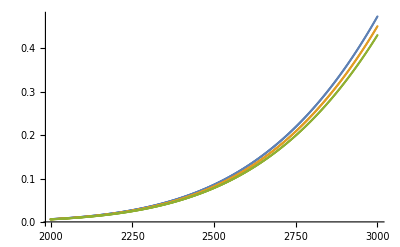

```mathematica
sub[cvac_,list_]:=Transpose[{Transpose[list][[1]],(100/(100+cvac))*Transpose[list][[2]]}]
ListPlot[{sub[0,concU4][[1;;-1]],sub[5,concU4][[1;;-1]],sub[10,concU4][[1;;-1]]}]
```

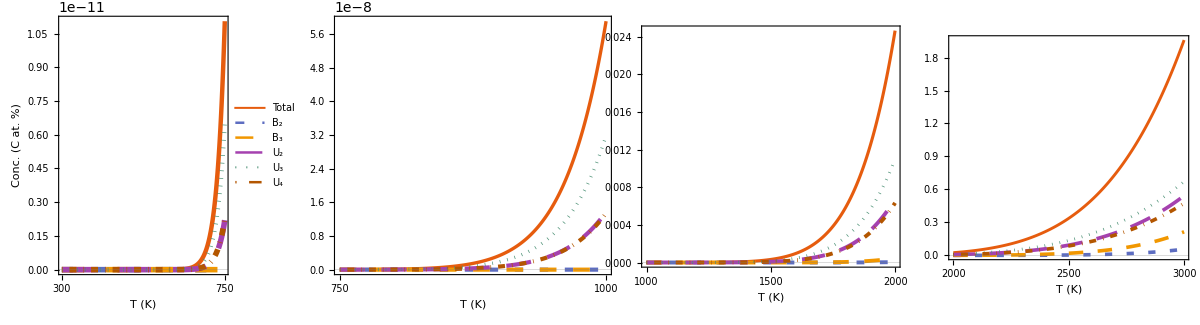

```mathematica
concDefects=GraphicsGrid[{{p0,p1,p2,p3}},ImageSize->1200,Spacings->-25]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/concDefects.pdf",concDefects]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/concDefects.pdf

#### Log defects

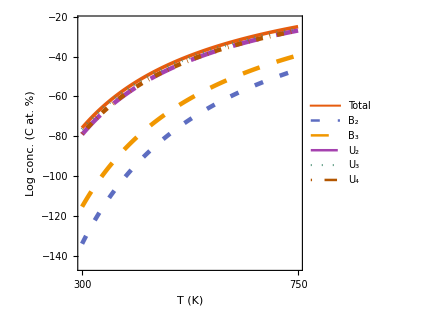

```mathematica
upper=750;
lower=300;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,Log[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concU2=Transpose@{rangeT,Log[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,Log[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,Log[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concTotal=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]+100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]+100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
l0=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["Log conc. (C at. %)",18,Black]},Frame->True,ImageSize->320,PlotTheme->Scientific,PlotLegends->Placed[{Style["Total",18,Black],Style["B_2",18,Black],Style["B_3",18,Black],Style["U_2",18,Black],Style["U_3",18,Black],Style["U_4",18,Black]},{0.75,0.32}],AspectRatio->1,PlotRange->{Automatic,{-145,-22}},FrameTicks->{{Automatic,None},{{300,750},None}}]
```

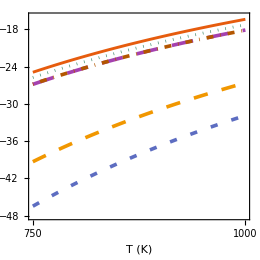

```mathematica
upper=1000;
lower=750;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,Log[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concU2=Transpose@{rangeT,Log[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,Log[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,Log[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concTotal=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]+100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]+100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
l1=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["",18,Black]},Frame->True,ImageSize->260,PlotTheme->Scientific,AspectRatio->1,PlotRange->{Automatic,{-48,-16}},FrameTicks->{{Automatic,None},{{750,1000},None}}]
```

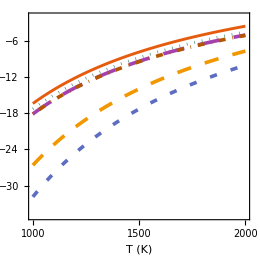

```mathematica
upper=2000;
lower=1000;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,Log[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concU2=Transpose@{rangeT,Log[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,Log[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,Log[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concTotal=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]+100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]+100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
l2=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["",18,Black]},Frame->True,ImageSize->260,AspectRatio->1,PlotRange->{Automatic,{-35,-2}},FrameTicks->{{Automatic,None},{{1000,1500,2000},None}}]
```

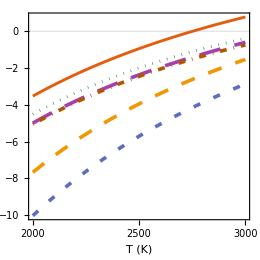

```mathematica
upper=3000;
lower=2000;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,Log[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concU2=Transpose@{rangeT,Log[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,Log[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,Log[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concTotal=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]+100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]+100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
l3=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["",18,Black]},Frame->True,ImageSize->260,AspectRatio->1,PlotRange->All,FrameTicks->{{Automatic,None},{{2000,2500,3000},None}}]
```

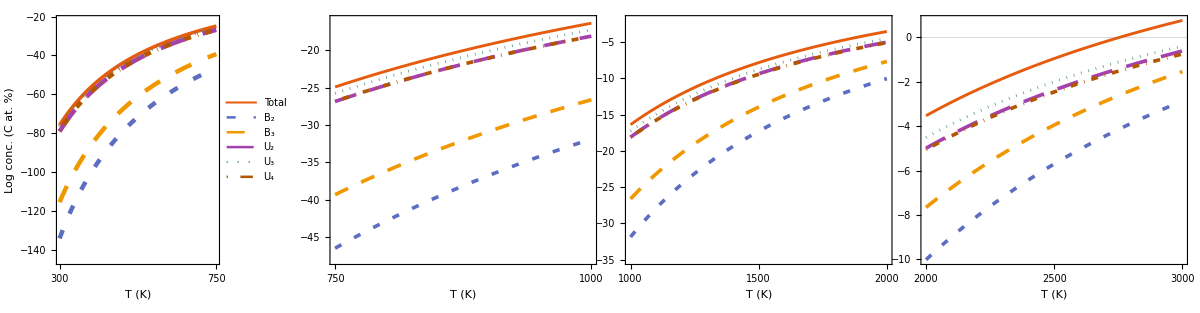

```mathematica
logConcDefects=GraphicsGrid[{{l0,l1,l2,l3}},ImageSize->1200,Spacings->-15]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/logConcDefects.pdf",logConcDefects]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/logConcDefects.pdf

#### Mixed log and normal conc defects

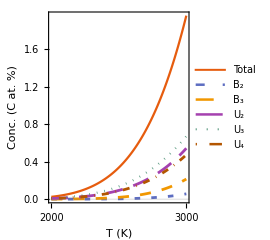

```mathematica
upper=3000;
lower=2000;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};
q1=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotLegends->Placed[{Style["Total",18,Black],Style["B_2",18,Black],Style["B_3",18,Black],Style["U_2",18,Black],Style["U_3",18,Black],Style["U_4",18,Black]},{0.25,0.55}],PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["Conc. (C at. %)",18,Black]},Frame->True,ImageSize->{200,200},AspectRatio->1.2,PlotRange->All,FrameTicks->{{Automatic,None},{{2000,2500,3000},None}}]
```

```mathematica
styles;
```

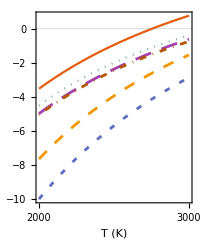

```mathematica
upper=3000;
lower=2000;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,Log[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concU2=Transpose@{rangeT,Log[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,Log[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,Log[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concTotal=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]+100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]+100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
q2=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["Log conc. (C at. %)",18,Black]},Frame->True,ImageSize->{200,186},AspectRatio->1.2,PlotRange->All,FrameTicks->{{Automatic,None},{{2000,2500,3000},None}}]
```

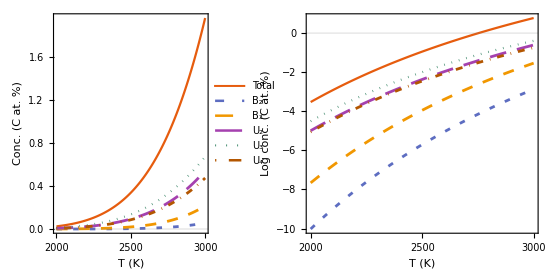

```mathematica
concDefectsLog=GraphicsGrid[{{q1,q2}},Spacings->-30,ImageSize->550]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/concDefectsLog.pdf",concDefectsLog]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/concDefectsLog.pdf